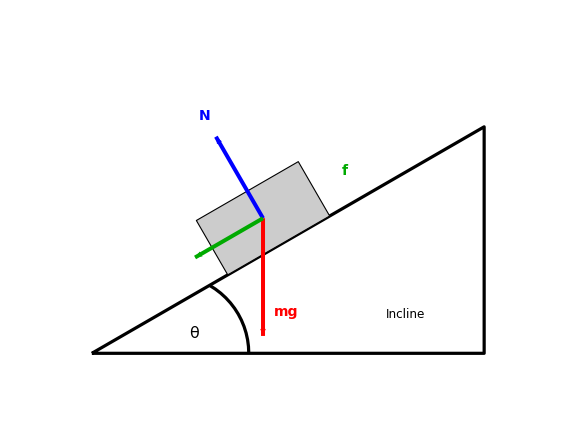

```mathematica
Graphics[{(*Define the incline angle*)θ=30 Degree;
(*Draw the Inclined Plane*)Thickness[0.004],Line[{{0,0},{5,0},{5,5 Tan[θ]},{0,0}}],(*Draw the Cart (rotated to match incline)*)Rotate[{EdgeForm[Black],GrayLevel[0.8],Rectangle[{2,0},{3.5,0.8}],Black},θ,{0,0}],(*Force Vectors (originating from center of mass)*){Thickness[0.005],Blue,Arrowheads[0.03],(*Center of mass position*)With[{com=RotationTransform[θ,{0,0}][{2.75,0.4}]},{(*Gravity:mg*)Red,Arrow[{com,com+{0,-1.5}}],Text[Style["mg",14,Bold],com+{0.3,-1.2}],(*Normal Force:N*)Blue,Arrow[{com,com+RotationTransform[θ+90 Degree,{0,0}][{1.2,0}]}],Text[Style["N",14,Bold],com+RotationTransform[θ+90 Degree,{0,0}][{1.5,0}]],(*Friction Force:f*)Darker[Green],Arrow[{com,com+RotationTransform[θ+180 Degree,{0,0}][{1.0,0}]}],Text[Style["f",14,Bold],com+RotationTransform[θ+180 Degree,{0,0}][{-1.2,0}]]}]},(*Angle Theta*)Circle[{1,0},1,{2*θ,0}],Text[Style["θ",16],{1.3,0.25}],(*Labels*)Text[Style["Incline",12,Italic],{4,0.5}]},PlotRange->{{-0.5,5.5},{-0.5,4}},ImageSize->Large]
```

#### Problem 4.

Best Fit Parameters: {a→12.4092,mu→7.49934,sigma→0.899733}

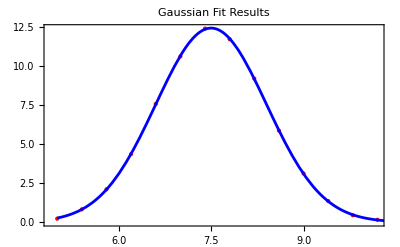

```mathematica
(*1. Clear variables to avoid conflicts*)Clear[x,a,mu,sigma,xData,yData,data,nlp,model];

(*2. Define the data*)
xData={5.0,5.4,5.8,6.2,6.6,7.0,7.4,7.8,8.2,8.6,9.0,9.4,9.8,10.2};
yData={0.22,0.82,2.10,4.35,7.56,10.60,12.38,11.70,9.18,5.85,3.11,1.35,0.44,0.15};
data=Transpose[{xData,yData}];

(*3. Define the model and perform the fit*)
model=a*Exp[-(x-mu)^2/(2*sigma^2)];

(*We provide explicit starting values to help the solver*)
nlp=NonlinearModelFit[data,{model,sigma>0},{{a,12},{mu,7.5},{sigma,1}},x];

(*4. Output the results*)
Print["Best Fit Parameters: ",nlp["BestFitParameters"]];

(*5. Visualize*)
Show[ListPlot[data,PlotStyle->{Red,PointSize[Large]},PlotLabel->"Gaussian Fit Results"],Plot[nlp[x],{x,5,10.5},PlotStyle->Blue],Frame->True,Axes->False]
```

#### Problem 5.

{n0→851.96,lambda→0.214838,bkg→45.0613}

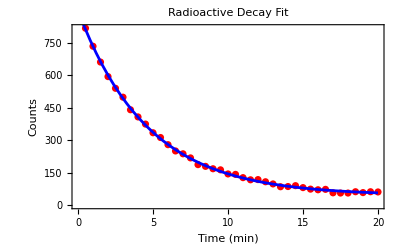

3.22637

```mathematica
Clear[t,counts,data,model,nlp,N0,lambda,bkg];

(*Time intervals from 0.5 to 20 in steps of 0.5*)
tData=Range[0.5,20.0,0.5];

(*Count data from the image*)
counts={816,733,660,593,539,498,440,407,374,334,312,279,250,237,218,187,179,168,163,144,142,127,117,118,108,98,85,86,90,81,74,71,73,57,56,56,62,58,62,61};

data=Transpose[{tData,counts}];
model=n0*Exp[-lambda*t]+bkg;

nlp=NonlinearModelFit[data,model,{{n0,900},{lambda,0.1},{bkg,60}},t];

(*Extract the results*)
nlp["BestFitParameters"]
Show[ListPlot[data,PlotStyle->Red,PlotLabel->"Radioactive Decay Fit"],Plot[nlp[t],{t,0,20},PlotStyle->Blue],Frame->True,FrameLabel->{"Time (min)","Counts"}]
Log[2]/(lambda/. nlp["BestFitParameters"])
```